```mathematica
Solve[{fϕNN+fϕprNN+fϕprprNN+fωNN+fωprNN+fωprprNN==F0&&mϕ^2 fϕNN+mϕpr^2 fϕprNN+mϕprpr^2+fϕ}]
```

{{fωprprNN→-(-fϕNN mϕ^2-fϕprNN mϕpr^2+(-F0+fϕNN+fϕprNN+fωNN+fωprNN) mϕprpr^2-fωNN mω^2-fωprNN mωpr^2)/(mϕprpr^2-mωprpr^2),fϕprprNN→-(fϕNN mϕ^2+fϕprNN mϕpr^2+fωNN mω^2+fωprNN mωpr^2+F0 mωprpr^2-fϕNN mωprpr^2-fϕprNN mωprpr^2-fωNN mωprpr^2-fωprNN mωprpr^2)/(mϕprpr^2-mωprpr^2)}}

```mathematica
FormFactorIsoscalar[t_]=Sum[m[a,i]^2/(m[a,i]^2-t)f[a,i]*ToExpression["f"<>s1s2[a]<>pr[i]],{a,{p,w}},{i,{0,1,2}}]
repl[expr_]:=expr/.Flatten[Table[{ToExpression["f"<>s1s2[part]<>pr[i]]->1},{part,{w,p,r}},{i,0,2}]]
solIsoscalar1=Solve[{repl[Sum[f[a,i],{a,{p,w}},{i,{0,1,2}}]]==F01s&&repl[Sum[m[a,i]^2 f[a,i],{a,{p,w}},{i,{0,1,2}}]]==0},{fωprprNN,fϕprprNN}][[1]]//Simplify;
solIsoscalar2=Solve[{repl[Sum[f[a,i],{a,{p,w}},{i,{0,1,2}}]]==F02s&&repl[Sum[m[a,i]^2 f[a,i],{a,{p,w}},{i,{0,1,2}}]]==0&&repl[Sum[m[a,i]^4 f[a,i],{a,{p,w}},{i,{0,1,2}}]]==0},{fωprprNN,fϕprprNN,fωprNN}][[1]]//Simplify
FormFactorIsoscalar1[t_]=FormFactorIsoscalar[t]/.solIsoscalar1//Simplify;
FormFactorIsoscalar1[t_]=Sum[ToExpression["f"<>s1s2[a]<>pr[i]<>"NN"]/ToExpression["f"<>s1s2[a]<>pr[i]]*D[FormFactorIsoscalar1[t],ToExpression["f"<>s1s2[a]<>pr[i]<>"NN"]],{a,{p,w}},{i,{0,1}}]
FormFactorIsoscalar2[t_]=FormFactorIsoscalar[t]/.solIsoscalar2//Simplify;
FormFactorIsoscalar2[t_]=Sum[ToExpression["f"<>s1s2[a]<>pr[i]<>"NN"]/ToExpression["f"<>s1s2[a]<>pr[i]]*D[FormFactorIsoscalar1[t],ToExpression["f"<>s1s2[a]<>pr[i]<>"NN"]],{a,{p,w}},{i,{0,1}}]
```

(fϕNN mϕ^2)/(mϕ^2-t)+(fϕprNN mϕpr^2)/(mϕpr^2-t)+(fϕprprNN mϕprpr^2)/(mϕprpr^2-t)+(fωNN mω^2)/(mω^2-t)+(fωprNN mωpr^2)/(mωpr^2-t)+(fωprprNN mωprpr^2)/(mωprpr^2-t)

{fωprprNN→(-fωNN mϕprpr^2 mω^2+fωNN mω^4-F02s mϕprpr^2 mωpr^2+fωNN mϕprpr^2 mωpr^2-fωNN mω^2 mωpr^2+fϕNN (mϕ^2-mϕprpr^2) (mϕ^2-mωpr^2)+fϕprNN (mϕpr^2-mϕprpr^2) (mϕpr^2-mωpr^2))/((mϕprpr^2-mωprpr^2) (-mωpr^2+mωprpr^2)),fϕprprNN→(-fωNN mω^4+fωNN mω^2 mωpr^2+fωNN mω^2 mωprpr^2+F02s mωpr^2 mωprpr^2-fωNN mωpr^2 mωprpr^2-fϕNN (mϕ^2-mωpr^2) (mϕ^2-mωprpr^2)-fϕprNN (mϕpr^2-mωpr^2) (mϕpr^2-mωprpr^2))/((mϕprpr^2-mωpr^2) (mϕprpr^2-mωprpr^2)),fωprNN→(-fωNN mϕprpr^2 mω^2+fωNN mω^4-F02s mϕprpr^2 mωprpr^2+fωNN mϕprpr^2 mωprpr^2-fωNN mω^2 mωprpr^2+fϕNN (mϕ^2-mϕprpr^2) (mϕ^2-mωprpr^2)+fϕprNN (mϕpr^2-mϕprpr^2) (mϕpr^2-mωprpr^2))/((mϕprpr^2-mωpr^2) (mωpr^2-mωprpr^2))}

(fϕNN (mϕ^2/(mϕ^2-t)+(mϕprpr^2 (-mϕ^2+mωprpr^2))/((mϕprpr^2-mωprpr^2) (mϕprpr^2-t))-((-mϕ^2+mϕprpr^2) mωprpr^2)/((mϕprpr^2-mωprpr^2) (mωprpr^2-t))))/fϕ+(fϕprNN (mϕpr^2/(mϕpr^2-t)+(mϕprpr^2 (-mϕpr^2+mωprpr^2))/((mϕprpr^2-mωprpr^2) (mϕprpr^2-t))-((-mϕpr^2+mϕprpr^2) mωprpr^2)/((mϕprpr^2-mωprpr^2) (mωprpr^2-t))))/fϕpr+(fωNN ((mϕprpr^2 (-mω^2+mωprpr^2))/((mϕprpr^2-mωprpr^2) (mϕprpr^2-t))+mω^2/(mω^2-t)-((mϕprpr^2-mω^2) mωprpr^2)/((mϕprpr^2-mωprpr^2) (mωprpr^2-t))))/fω+(fωprNN ((mϕprpr^2 (-mωpr^2+mωprpr^2))/((mϕprpr^2-mωprpr^2) (mϕprpr^2-t))+mωpr^2/(mωpr^2-t)-((mϕprpr^2-mωpr^2) mωprpr^2)/((mϕprpr^2-mωprpr^2) (mωprpr^2-t))))/fωpr

## Definitions

```mathematica
f[r,0]
```

fρNN/fρ

```mathematica
{μp,μn}={2.792,-1.913};
listsymbols={mϕ,mϕpr,mϕprpr,mω,mωpr,mωprpr,Γϕ,Γϕpr,Γϕprpr,Γω,Γωpr,Γωprpr,mρ,mρpr,mρprpr,Γρ,Γρpr,Γρprpr}
listsymbolsvals=ToExpression[ToString[#]<>"val"]&/@listsymbols;
MapThread[(#1["Central"]=#2)&,{listsymbolsvals,{1.019461,1.68,2.164,0.782,1.41,1.67,0.004249,0.15,0.106,0.00868,0.29,0.315,0.77526,1.465,1.72,0.1474,0.4,0.25}}];
MapThread[(#1["Upper"]=#2)&,{listsymbolsvals,{1.019461+0.016*10^-3,1.7,2.17,0.782+0.13*10^-3,1.47,1.7,0.004249,0.2,0.13,0.00868+0.13*10^-3,0.48,0.35,0.77526+0.23*10^-3,1.485,1.74,0.1474+0.8*10^-3,0.46,0.35}}];
MapThread[(#1["Lower"]=#2)&,{listsymbolsvals,{1.019461-0.016*10^-3,1.66,2.158,0.782-0.13*10^-3,1.35,1.64,0.004249,0.1,0.088,0.00868-0.13*10^-3,0.1,0.28,0.77526-0.23*10^-3,1.445,1.7,0.1474-0.8*10^-3,0.34,0.15}}];
SortBy[Flatten[Table[{listsymbols[[i]],unc,ToExpression[ToString[listsymbols[[i]]]<>"val"][unc]},{i,1,Length[listsymbols],1},{unc,{"Lower","Central","Upper"}}],1],#[[1]]&]//TableForm
{pr[0],pr[1],pr[2]}={"","pr","prpr"};
mthr[s1_,q_,s2_]:=MapThread[(q[s1,#1]=ToExpression[ToString[q]<>s2<>#2])&,{{0,1,2},pr[#]&/@Range[0,2]}];
mthr1[s1_,s2_]:=MapThread[(f[s1,#1]=ToExpression["f"<>s2<>#2<>"NN"]/ToExpression["f"<>s2<>#2])&,{{0,1,2},pr[#]&/@Range[0,2]}];
{s1s2[w],s1s2[p],s1s2[r]}={"ω","ϕ","ρ"};
Do[
Do[
mthr[P,q,s1s2[P]]
,{q,{m,Γ}}];
mthr1[P,s1s2[P]]
,{P,{w,p,r}}]
```

{mϕ,mϕpr,mϕprpr,mω,mωpr,mωprpr,Γϕ,Γϕpr,Γϕprpr,Γω,Γωpr,Γωprpr,mρ,mρpr,mρprpr,Γρ,Γρpr,Γρprpr}

mρ | Central | 0.77526
mρ | Lower | 0.77503
mρ | Upper | 0.77549
mρpr | Central | 1.465
mρpr | Lower | 1.445
mρpr | Upper | 1.485
mρprpr | Central | 1.72
mρprpr | Lower | 1.7
mρprpr | Upper | 1.74
mϕ | Central | 1.01946
mϕ | Lower | 1.01945
mϕ | Upper | 1.01948
mϕpr | Central | 1.68
mϕpr | Lower | 1.66
mϕpr | Upper | 1.7
mϕprpr | Central | 2.164
mϕprpr | Lower | 2.158
mϕprpr | Upper | 2.17
mω | Central | 0.782
mω | Lower | 0.78187
mω | Upper | 0.78213
mωpr | Central | 1.41
mωpr | Lower | 1.35
mωpr | Upper | 1.47
mωprpr | Central | 1.67
mωprpr | Lower | 1.64
mωprpr | Upper | 1.7
Γρ | Central | 0.1474
Γρ | Lower | 0.1466
Γρ | Upper | 0.1482
Γρpr | Central | 0.4
Γρpr | Lower | 0.34
Γρpr | Upper | 0.46
Γρprpr | Central | 0.25
Γρprpr | Lower | 0.15
Γρprpr | Upper | 0.35
Γϕ | Central | 0.004249
Γϕ | Lower | 0.004249
Γϕ | Upper | 0.004249
Γϕpr | Central | 0.15
Γϕpr | Lower | 0.1
Γϕpr | Upper | 0.2
Γϕprpr | Central | 0.106
Γϕprpr | Lower | 0.088
Γϕprpr | Upper | 0.13
Γω | Central | 0.00868
Γω | Lower | 0.00855
Γω | Upper | 0.00881
Γωpr | Central | 0.29
Γωpr | Lower | 0.1
Γωpr | Upper | 0.48
Γωprpr | Central | 0.315
Γωprpr | Lower | 0.28
Γωprpr | Upper | 0.35

### Compact definitions for form factors

```mathematica
(*Squared masses difference*)
Δ[p1_,o1_,p2_,o2_]:=m[p1,o1]^2-m[p2,o2]^2
(*Product of two pole terms times the squared mass difference - numerously enters the expression for the form factors*)
d[p1_,o1_,p2_,o2_]:=(m[p1,o1]^2 m[p2,o2]^2)/((m[p1,o1]^2-t)(m[p2,o2]^2-t))Δ[p1,o1,p2,o2]
(*Product of two pole terms - numerously enters the expression for the form factors*)
d1[p1_,o1_,p2_,o2_]:=(m[p1,o1]^2 m[p2,o2]^2)/((m[p1,o1]^2-t)(m[p2,o2]^2-t))
(*Product of three pole terms times the squared mass difference - numerously enters the expression for the form factors*)
d[p1_,o1_,p2_,o2_,p3_,o3_]:=(m[p1,o1]^2 m[p2,o2]^2 m[p3,o3]^2)/((m[p1,o1]^2-t)(m[p2,o2]^2-t)(m[p3,o3]^2-t))Δ[p1,o1,p2,o2]*Δ[p3,o3,p2,o2]
(*Product of two pole terms - numerously enters the expression for the form factors*)
d1[p1_,o1_,p2_,o2_,p3_,o3_]:=(m[p1,o1]^2 m[p2,o2]^2 m[p3,o3]^2)/((m[p1,o1]^2-t)(m[p2,o2]^2-t)(m[p3,o3]^2-t))
```

### Analytic continuation to get form-factors on the whole plane -∞<t<∞

```mathematica
(*Conformally transformed t*)
V[t_]=I(√(√((tin-t0)/t0)+√((t-t0)/t0))-√(√((tin-t0)/t0)-√((t-t0)/t0)))/(√(√((tin-t0)/t0)+√((t-t0)/t0))+√(√((tin-t0)/t0)-√((t-t0)/t0)));
{VrSmallm[m2_],VrcSmallm[m2_]}={1,-1}V[m2];
VrLargem[m2_]=V[m2]/.{√(√((tin-t0)/t0)-√((m2-t0)/t0))->I*√(√((m2-t0)/t0)-√((tin-t0)/t0))};
VrcLargem[m2_]=-V[m2]/.{√(√((tin-t0)/t0)-√((m2-t0)/t0))->-I*√(√((m2-t0)/t0)-√((tin-t0)/t0))};
VrLargem[m2]*VrcLargem[m2]//Simplify
ctransform[v_]=t0-4(tin-t0)/(1/v-v)^2//Simplify;
(*Expressing Subscript[m, meson],Subscript[t, 0] in terms of Subscript[v, R] == v(Subscript[m^2, meson]), Subscript[v, N] == v(0)*)
solmtin=Solve[{m2==ctransform[vR]&&0==ctransform[vN]},{m2,tin}][[1]];
Print["m^2 and t_in in terms of v_N = v(0), v_R = v(m^2):"]
{m2sol,tinsol}={m2,tin}/.solmtin;
m2sol=Factor[m2sol];
{m2sol,tinsol}
Print["Expressions for m^2 - analytic continuation v(m^2)->v(z) (compare to Eqs. for C_s from https://arxiv.org/pdf/1601.06190, e.q., Eq. (40)):"]
m2solSmallm=Factor[m2sol]/.{vN*vR+1->(1-vN*vRc),vN+vR->vN-vRc,vR+1->1-vRc}//Simplify;
m2solLargem=Simplify[(Factor[m2sol]/.{vN*vR-1->1/vRc(vN-vRc),vN*vR+1->1/vRc(vN+vRc)})]/.{(vR+1)->1/(√vRc)√((1+vRc)(1+vR)),(vR-1)->1/(√vRc)√((1-vRc)(vR-1))};
{{"m^2(m^2<t_in)","m^2(m^2>t_in)"},{m2solSmallm,m2solLargem}}//TableForm
Print["Check that they are reduced to m^2 if inserting v_R(m^2), v_R_c(m^2):"]
Assuming[tin>t0>0&&m2>t0,Simplify[{m2solSmallm/.{vN->V[0],vR->VrSmallm[m2],vRc->VrcSmallm[m2]},m2solLargem/.{vN->V[0],vR->VrLargem[m2],vRc->VrcLargem[m2]}}]]//Cancel
Print["m^2/m^2 in terms of v(t), v_N = v(0), v_R = v(m^2):"]
poleterm=Factor[m2/(m2-t)/.{t->ctransform[v]}/.{m2->m2sol,tin->tinsol}//FullSimplify]
Print["Checking if the expression matches Eq. (30) of https://arxiv.org/pdf/1601.06190"]
poleterm-((1-v^2)/(1-vN^2))^2*((vN-vR)(vN+vR)(vN-1/vR)(vN+1/vR))/((v-vR)(v+vR)(v-1/vR)(v+1/vR))//Expand//Together//Simplify
Print["Pole terms - analytically continued using v_R = -(v^*)_R or v_R = 1/(v^*)_R (compare to Eqs. (34), (35) from the screenshot below):"]
poletermSmallm=poleterm/.{vN+vR->vN-vRc,1+vN*vR->1-vN*vRc,v+vR->v-vRc,1+v*vR->1-v*vRc}//Simplify;
poletermLargem=poleterm/.{-1+vN*vR->1/vRc(-vRc+vN),1+vN*vR->1/vRc(vRc+vN),1+v*vR->1/vRc(vRc+v),-1+v*vR->1/vRc(-vRc+v)}//Simplify;
{{"m^2<t_in","m^2>t_in"},{poletermSmallm,poletermLargem}}//TableForm
```

1

m^2 and t_in in terms of v_N = v(0), v_R = v(m^2):

{-(t0 (vN-vR) (vN+vR) (vN vR-1) (vN vR+1))/(vN^2 (vR-1)^2 (vR+1)^2),(t0 (vN^4+2 vN^2+1))/(4 vN^2)}

Expressions for m^2 - analytic continuation v(m^2)->v(z) (compare to Eqs. for C_s from https://arxiv.org/pdf/1601.06190, e.q., Eq. (40)):

m^2(m^2<t_in) | m^2(m^2>t_in)
(t0 (vN-vR) (vN vR-1) (vN-vRc) (vN vRc-1))/(vN^2 (vR-1)^2 (vRc-1)^2) | -(t0 (vN-vR) (vN+vR) (vN-vRc) (vN+vRc))/(vN^2 (vR-1) (vR+1) (1-vRc) (vRc+1))

Check that they are reduced to m^2 if inserting v_R(m^2), v_R_c(m^2):

{m2,m2}

m^2/m^2 in terms of v(t), v_N = v(0), v_R = v(m^2):

((v-1)^2 (v+1)^2 (vN-vR) (vN+vR) (vN vR-1) (vN vR+1))/((vN-1)^2 (vN+1)^2 (v-vR) (v+vR) (v vR-1) (v vR+1))

Checking if the expression matches Eq. (30) of https://arxiv.org/pdf/1601.06190

0

Pole terms - analytically continued using v_R = -(v^*)_R or v_R = 1/(v^*)_R (compare to Eqs. (34), (35) from the screenshot below):

m^2<t_in | m^2>t_in
((v^2-1)^2 (vN-vR) (vN vR-1) (vN-vRc) (vN vRc-1))/((vN^2-1)^2 (v-vR) (v vR-1) (v-vRc) (v vRc-1)) | ((v^2-1)^2 (vN-vR) (vN+vR) (vN-vRc) (vN+vRc))/((vN^2-1)^2 (v-vR) (v+vR) (v-vRc) (v+vRc))

-Graphics-

#### Analytically continued expressions for m^2/(m^2-t) and m^2

```mathematica
(*Depending on the relationship between m^2-Γ^2/2 and Subscript[t, in], get explicit expression for different quantities in terms of t - now, analytically continued*)
(*m^2/(m^2-t)*)
poleTermRepl[small_,part_,o_]:=Block[{},
If[small,
poletermSmallm/.{vR->VrSmallm[(m[part,o]-I*Γ[part,o]/2)^2],vRc->VrcSmallm[(m[part,o]+I*Γ[part,o]/2)^2]}
,
poletermLargem/.{vR->VrLargem[(m[part,o]-I*Γ[part,o]/2)^2],vRc->VrcLargem[(m[part,o]+I*Γ[part,o]/2)^2]}
]/.{v->V[t]}/.{vN->V[0]}
]
dtransformed[part_,o_,diracpauli_]:=Block[{pstr,expr},
pstr=ToString[part];
If[diracpauli==1,
If[(o==0&&MemberQ[{"w","p"},pstr])||pstr=="r",
expr=poleTermRepl[True,part,o]
,
expr=poleTermRepl[False,part,o]
];
];
If[diracpauli==2,
If[(o==0&&MemberQ[{"w","p"},pstr])||(pstr=="r"&&o!=2),
expr=poleTermRepl[True,part,o]
,
expr=poleTermRepl[False,part,o]
];
];
t0v=If[pstr=="r",4,9]*mπ^2;
expr=expr/.{t0->t0v,tin->ToExpression[ToString[tin]<>ToString[diracpauli]<>If[pstr=="r","v","s"]]};
expr
]
(*m^2*)
m2Repl[small_,part_,o_]:=Block[{},
If[small,
m2solSmallm/.{vR->VrSmallm[(m[part,o]-I*Γ[part,o]/2)^2],vRc->VrcSmallm[(m[part,o]+I*Γ[part,o]/2)^2]}
,
m2solLargem/.{vR->VrLargem[(m[part,o]-I*Γ[part,o]/2)^2],vRc->VrcLargem[(m[part,o]+I*Γ[part,o]/2)^2]}
]/.{vN->V[0]}
]
m2transformed[part_,o_,diracpauli_]:=Block[{expr,pstr},
pstr=ToString[part];
(*Decision if using the replacement for m^2<Subscript[t, in] or m^2>Subscript[t, in], based on a priori assumed relations from 1601...*)
If[diracpauli==1,
If[(o==0&&MemberQ[{"w","p"},pstr])||pstr=="r",
expr=m2Repl[True,part,o]
,
expr=m2Repl[False,part,o]
]
];
If[diracpauli==2,
If[(o==0&&MemberQ[{"w","p"},pstr])||(pstr=="r"&&o!=2),
expr=m2Repl[True,part,o]
,
expr=m2Repl[False,part,o]
];
];
t0v=If[pstr=="r",4,9]*mπ^2;
expr=expr/.{t0->t0v,tin->ToExpression[ToString[tin]<>ToString[diracpauli]<>If[pstr=="r","v","s"]]};
expr
]
Do[
dconf[p1,o1,diracpauli]=dtransformed[p1,o1,diracpauli]//Simplify;
m2conf[p1,o1,diracpauli]=m2transformed[p1,o1,diracpauli]//Simplify
,{p1,{r,p,w}},{o1,{0,1,2}},{diracpauli,{1,2}}]//AbsoluteTiming
(*The same as in section "Compact definitions for form factors"*)
Δc[p1_,o1_,p2_,o2_,diracpauli_]:=(m2conf[p1,o1,diracpauli]-m2conf[p2,o2,diracpauli])(*Δ[p1,o1,p2,o2]*)
dc[p1_,o1_,p2_,o2_,diracpauli_]:=dconf[p1,o1,diracpauli]*dconf[p2,o2,diracpauli]*Δc[p1,o1,p2,o2,diracpauli]
d1c[p1_,o1_,p2_,o2_,diracpauli_]:=dconf[p1,o1,diracpauli]*dconf[p2,o2,diracpauli]
dc[p1_,o1_,p2_,o2_,p3_,o3_,diracpauli_]:=dconf[p1,o1,diracpauli]*dconf[p2,o2,diracpauli]*dconf[p3,o3,diracpauli]*Δc[p1,o1,p2,o2,diracpauli]*Δc[p3,o3,p2,o2,diracpauli]
d1c[p1_,o1_,p2_,o2_,p3_,o3_,diracpauli_]:=dconf[p1,o1,diracpauli]*dconf[p2,o2,diracpauli]*dconf[p3,o3,diracpauli]
```

{0.781248,Null}

## Form factors

### No analytic continuation

```mathematica
(*Compare to Eqs. (24)-(27)*)
F1["s",t_,a_]=F1s0*d1[w,2,p,2]+(d[p,2,w,1]*1/Δ[p,2,w,2]+d[w,2,w,1] 1/Δ[w,2,p,2]-d1[w,2,p,2])*f[w,1]+(d[p,2,p,1] 1/Δ[p,2,w,2]+d[w,2,p,1] 1/Δ[w,2,p,2]-d1[w,2,p,2])*f[p,1]+(d[p,2,w,0] 1/Δ[p,2,w,2]+d[w,2,w,0] 1/Δ[w,2,p,2]-d1[w,2,p,2])f[w,0]+(d[p,2,p,0] 1/Δ[p,2,w,2]+d[w,2,p,0] 1/Δ[w,2,p,2]-d1[w,2,p,2])f[p,0];
F1["v",t_,a_]=F1v0*d1[r,2,r,1]+(d[r,1,r,0] 1/Δ[r,1,r,2]+d[r,2,r,0] 1/Δ[r,2,r,1]-d1[r,2,r,1])f[r,0];
F2["s",t_,a_]=
F2s0*d1[w,2,p,2,w,1]+(d[p,2,p,1,w,1] 1/(Δ[p,2,w,2]*Δ[w,1,w,2])+d[w,2,p,1,w,1] 1/(Δ[w,2,p,2]*Δ[w,1,p,2])+d[w,2,p,1,p,2] 1/(Δ[w,2,w,1]*Δ[p,2,w,1])-d1[w,2,p,2,w,1])f[p,1]+(d[p,2,w,0,w,1] 1/(Δ[p,2,w,2]*Δ[w,1,w,2])+d[w,2,w,0,w,1] 1/(Δ[w,2,p,2]*Δ[w,1,p,2])+d[w,2,w,0,p,2] 1/(Δ[w,2,w,1]*Δ[p,2,w,1])-d1[w,2,p,2,w,1])f[w,0]+(d[p,2,p,0,w,1] 1/(Δ[p,2,w,2]*Δ[w,1,w,2])+d[w,2,p,0,w,1] 1/(Δ[w,2,p,2]*Δ[w,1,p,2])+d[w,2,p,0,p,2] 1/(Δ[w,2,w,1]*Δ[p,2,w,1])-d1[w,2,p,2,w,1])f[p,0];
F2["v",t_,a_]=F2v0*d1[r,2,r,1,r,0];
Print["Values at t = 0:"]
Flatten[Table[{Subscript["F",ToString[i]<>","<>v],ToExpression["F"<>ToString[i]][v,0,a]//Simplify},{i,1,2,1},{v,{"s","v"}}],1]
Print["Asymptotics at t -> Infinity:"]
Flatten[Table[{Subscript["F",ToString[i]<>","<>v],Total[(1/t^# Simplify[Limit[ToExpression["F"<>ToString[i]][v,t,a] t^#,t->Infinity]])&/@Select[{1,2,3},#<i+2&]]},{i,1,2,1},{v,{"s","v"}}],1]
```

Values at t = 0:

(F_(1,s) | F01s
F_(1,v) | F01v
F_(2,s) | F02s
F_(2,v) | F02v)

Asymptotics at t -> Infinity:

(F_(1,s) | (F01s mωprpr^2 mϕprpr^2+(fωNN (mω^2-mωprpr^2) (mϕprpr^2-mω^2))/fω+(fωprNN (mωpr^2-mωprpr^2) (mϕprpr^2-mωpr^2))/fωpr-(fϕNN (mϕ^2-mωprpr^2) (mϕ^2-mϕprpr^2))/fϕ-(fϕprNN (mϕpr^2-mωprpr^2) (mϕpr^2-mϕprpr^2))/fϕpr)/t^2
F_(1,v) | (F01v mρpr^2 mρprpr^2-(fρNN (mρ^2-mρpr^2) (mρ^2-mρprpr^2))/fρ)/t^2
F_(2,s) | (-F02s mωpr^2 mωprpr^2 mϕprpr^2+(fωNN (mω^2-mωpr^2) (mω^2-mωprpr^2) (mϕprpr^2-mω^2))/fω-(fϕNN (mϕ^2-mωpr^2) (mϕ^2-mωprpr^2) (mϕ^2-mϕprpr^2))/fϕ-(fϕprNN (mϕpr^2-mωpr^2) (mϕpr^2-mωprpr^2) (mϕpr^2-mϕprpr^2))/fϕpr)/t^3
F_(2,v) | -(F02v mρ^2 mρpr^2 mρprpr^2)/t^3)

```mathematica
(*repl[expr_]:=expr/.Join[Flatten[Table[{ToExpression["f"<>s1s2[part]<>pr[i]]->1,m[part,i]^2->(m[part,i]-I*Γ[part,i]/2)^2},{part,{w,p,r}},{i,0,2}]],{mπ->0.139}]
pttt[t_]=F1["s",t,a]+F1["v",t,a];
F11["DP",t_,mρ_,mρpr_,mρprpr_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γρ_,Γρpr_,Γρprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_,F1s0_,F1v0_,fρNN_,fϕNN_,fϕprNN_,fωNN_,fωprNN_]=repl[pttt[t]];
F11["DP",t_]=F11["DP",t,mρval["Central"],mρprval["Central"],mρprprval["Central"],mϕval["Central"],mϕprval["Central"],mϕprprval["Central"],mωval["Central"],mωprval["Central"],mωprprval["Central"],Γρval["Central"],Γρprval["Central"],Γρprprval["Central"],Γϕval["Central"],Γϕprval["Central"],Γϕprprval["Central"],Γωval["Central"],Γωprval["Central"],Γωprprval["Central"],F01val["s","DP"],F01val["v","DP"],f1val[pt,r,0],f1val[pt,p,0],f1val[pt,p,1],f1val[pt,w,0],f1val[pt,w,1]];
pttt[t_]=F2["s",t,a]+F2["v",t,a];
F21["DP",t_,mρ_,mρpr_,mρprpr_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γρ_,Γρpr_,Γρprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_,F2s0_,F2v0_,fϕNN_,fϕprNN_,fωNN_]=repl[pttt[t]];
F21["DP",t_]=F21["DP",t,mρval["Central"],mρprval["Central"],mρprprval["Central"],mϕval["Central"],mϕprval["Central"],mϕprprval["Central"],mωval["Central"],mωprval["Central"],mωprprval["Central"],Γρval["Central"],Γρprval["Central"],Γρprprval["Central"],Γϕval["Central"],Γϕprval["Central"],Γϕprprval["Central"],Γωval["Central"],Γωprval["Central"],Γωprprval["Central"],F02val["s","DP"],F02val["v","DP"],f2val[pt,p,0],f2val[pt,p,1],f2val[pt,w,0]];
GEP[t_]=F11["DP",t]+t/(4*0.938^2)(F21["DP",t]);
LogPlot[{Abs[F11["DP",t^2]],Abs[F1Ritz[t]]},{t,0,2},ImageSize->Large,PlotRange->All,Frame->True]
LogPlot[{Abs[GEP[t^2]],Abs[F1Ritz[t]+t^2/(4*0.938^2)F2Ritz[t]]},{t,0,2},ImageSize->Large,Frame->True]*)
```

### Analytic continuation

```mathematica
F1conf["s",t_,a_]=F1s0*d1c[w,2,p,2,1]+(dc[p,2,w,1,1]*1/Δc[p,2,w,2,1]+dc[w,2,w,1,1] 1/Δc[w,2,p,2,1]-d1c[w,2,p,2,1])*f[w,1]+(dc[p,2,p,1,1] 1/Δc[p,2,w,2,1]+dc[w,2,p,1,1] 1/Δc[w,2,p,2,1]-d1c[w,2,p,2,1])*f[p,1]+(dc[p,2,w,0,1] 1/Δc[p,2,w,2,1]+dc[w,2,w,0,1] 1/Δc[w,2,p,2,1]-d1c[w,2,p,2,1])f[w,0]+(dc[p,2,p,0,1] 1/Δc[p,2,w,2,1]+dc[w,2,p,0,1] 1/Δc[w,2,p,2,1]-d1c[w,2,p,2,1])f[p,0];
F1conf["v",t_,a_]=F1v0*d1c[r,2,r,1,1]+(dc[r,1,r,0,1] 1/Δc[r,1,r,2,1]+dc[r,2,r,0,1] 1/Δc[r,2,r,1,1]-d1c[r,2,r,1,1])f[r,0];
F2conf["s",t_,a_]=F2s0*d1c[w,2,p,2,w,1,2]+(dc[p,2,p,1,w,1,2] 1/(Δc[p,2,w,2,2]*Δc[w,1,w,2,2])+dc[w,2,p,1,w,1,2] 1/(Δc[w,2,p,2,2]*Δc[w,1,p,2,2])+dc[w,2,p,1,p,2,2] 1/(Δc[w,2,w,1,2]*Δc[p,2,w,1,2])-d1c[w,2,p,2,w,1,2])f[p,1]+(dc[p,2,w,0,w,1,2] 1/(Δc[p,2,w,2,2]*Δc[w,1,w,2,2])+dc[w,2,w,0,w,1,2] 1/(Δc[w,2,p,2,2]*Δc[w,1,p,2,2])+dc[w,2,w,0,p,2,2] 1/(Δc[w,2,w,1,2]*Δc[p,2,w,1,2])-d1c[w,2,p,2,w,1,2])f[w,0]+(dc[p,2,p,0,w,1,2] 1/(Δc[p,2,w,2,2]*Δc[w,1,w,2,2])+dc[w,2,p,0,w,1,2] 1/(Δc[w,2,p,2,2]*Δc[w,1,p,2,2])+dc[w,2,p,0,p,2,2] 1/(Δc[w,2,w,1,2]*Δc[p,2,w,1,2])-d1c[w,2,p,2,w,1,2])f[p,0];
F2conf["v",t_,a_]=F2v0*d1c[r,2,r,1,r,0,2];
(*All fixed parameters inserted*)
repl[expr_]:=expr/.Join[Flatten[Table[{ToExpression["f"<>s1s2[part]<>pr[i]]->1},{part,{w,p,r}},{i,0,2}]],{mπ->0.139}]

F1conf["s",t_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_,F1s0_,fϕNN_,fϕprNN_,fωNN_,fωprNN_,tin1s_]=repl[F1conf["s",t,a]];
F1conf["v",t_,mρ_,mρpr_,mρprpr_,Γρ_,Γρpr_,Γρprpr_,F1v0_,fρNN_,fρprNN_,tin1v_]=repl[F1conf["v",t,a]];
F2conf["s",t_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_,F2s0_,fϕNN_,fϕprNN_,fωNN_,fωprNN_,tin2s_]=repl[F2conf["s",t,a]];
F2conf["v",t_,mρ_,mρpr_,mρprpr_,Γρ_,Γρpr_,Γρprpr_,F2v0_,fρNN_,fρprNN_,tin2v_]=repl[F2conf["v",t,a]];
```

```mathematica
D[F1conf["s",t,1.019,1.66,2.12,0.782,1.4,1.7,0.004,0.1,0.1,0.008,0.1,0.1,F1s0,fϕNN,fϕprNN,fωNN,fωprNN,1.046],fϕprNN]/.{t->2.1^2}
D[F1conf["s",t,1.019,1.66,2.12,0.782,1.4,1.7,0.004,0.1,0.1,0.008,0.1,0.1,F1s0,fϕNN,fϕprNN,fωNN,fωprNN,1.046],fϕNN]/.{t->2.1^2}
```

0.994532+1.42502 ⅈ

12.5557+17.85 ⅈ

## Case study - dark photon

### Isovector and isoscalar form-factors

```mathematica
pt="DP";
MapThread[(f1val[pt,w,#1]=#2)&,{{0,1},{1.5717,0.0418}}];
MapThread[(f1val[pt,p,#1]=#2)&,{{0,1},{-1.1247,0.1879}}];
MapThread[(f1val[pt,r,#1]=#2)&,{{0},{0.3747}}];
MapThread[(f2val[pt,w,#1]=#2)&,{{0},{-0.2096}}];
MapThread[(f2val[pt,p,#1]=#2)&,{{0,1},{0.2657,0.1781}}];
{tin1val["s"],tin2val["s"],tin1val["v"],tin2val["v"]}={1.0442,1.046,2.9506,2.3449};
{F01val["s",pt],F02val["s",pt],F01val["v",pt],F02val["v",pt]}={1/2,1/2(μp+μn-1),1/2,1/2(μp-μn-1)};
F1conf[pt,"s",t_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_]=F1conf["s",t,mϕ,mϕpr,mϕprpr,mω,mωpr,mωprpr,Γϕ,Γϕpr,Γϕprpr,Γω,Γωpr,Γωprpr,F01val["s",pt],f1val[pt,p,0],f1val[pt,p,1],f1val[pt,w,0],f1val[pt,w,1],tin1val["s"]];
F2conf[pt,"s",t_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_]=F2conf["s",t,mϕ,mϕpr,mϕprpr,mω,mωpr,mωprpr,Γϕ,Γϕpr,Γϕprpr,Γω,Γωpr,Γωprpr,F02val["s",pt],f2val[pt,p,0],f2val[pt,p,1],f2val[pt,w,0],f2val[pt,w,1],tin2val["s"]];
F1conf[pt,"v",t_,mρ_,mρpr_,mρprpr_,Γρ_,Γρpr_,Γρprpr_]=F1conf["v",t,mρ,mρpr,mρprpr,Γρ,Γρpr,Γρprpr,F01val["v",pt],f1val[pt,r,0],fρprNN,tin1val["v"]];
F2conf[pt,"v",t_,mρ_,mρpr_,mρprpr_,Γρ_,Γρpr_,Γρprpr_]=F2conf["v",t,mρ,mρpr,mρprpr,Γρ,Γρpr,Γρprpr,F02val["v",pt],f2val[pt,r,0],fρprNN,tin2val["v"]];
```

### Total form factors

```mathematica
valslist={mρval["Central"],mρprval["Central"],mρprprval["Central"],mϕval["Central"],mϕprval["Central"],mϕprprval["Central"],mωval["Central"],mωprval["Central"],mωprprval["Central"],Γρval["Central"],Γρprval["Central"],Γρprprval["Central"],Γϕval["Central"],Γϕprval["Central"],Γϕprprval["Central"],Γωval["Central"],Γωprval["Central"],Γωprprval["Central"]};
pt="DP";
F1total[pt,"Arbitrary",t_,mρ_,mρpr_,mρprpr_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γρ_,Γρpr_,Γρprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_]=F1totalTemp[t_,mρ_,mρpr_,mρprpr_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γρ_,Γρpr_,Γρprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_]=F1conf[pt,"s",t,mϕ,mϕpr,mϕprpr,mω,mωpr,mωprpr,Γϕ,Γϕpr,Γϕprpr,Γω,Γωpr,Γωprpr]+F1conf[pt,"v",t,mρ,mρpr,mρprpr,Γρ,Γρpr,Γρprpr];
F2total[pt,"Arbitrary",t_,mρ_,mρpr_,mρprpr_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γρ_,Γρpr_,Γρprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_]=F2totalTemp[t_,mρ_,mρpr_,mρprpr_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γρ_,Γρpr_,Γρprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_]=F2conf[pt,"s",t,mϕ,mϕpr,mϕprpr,mω,mωpr,mωprpr,Γϕ,Γϕpr,Γϕprpr,Γω,Γωpr,Γωprpr]+F2conf[pt,"v",t,mρ,mρpr,mρprpr,Γρ,Γρpr,Γρprpr];
{F1central[pt,t_],F2central[pt,t_]}={F1centralTemp[t_],F2centralTemp[t_]}=(#@@Join[{pt,"Arbitrary",t},valslist])&/@{F1total,F2total};
FFtab=Hold@Compile[{{massrange,_Complex}},{F1centralTemp[massrange],F2centralTemp[massrange]},CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True]/.DownValues@F1centralTemp/.DownValues@F2centralTemp//ReleaseHold;
massrange=Table[m,{m,-49.,49.,0.001}];
{F1centralInt[pt,t_],F2centralInt[pt,t_]}=With[{tab=FFtab[massrange]},Interpolation[Join[Partition[massrange,1],tab[[All,{#}]],2],InterpolationOrder->1][t]]&/@{1,2};//AbsoluteTiming
{Gep[t_],Gmp[t_]}={F1centralInt[pt,t]+t/(4*0.938^2)F2centralInt[pt,t],F1centralInt[pt,t]+F2centralInt[pt,t]};
```

{0.426986,Null}

### Plots

#### |F_1|,|F_2|

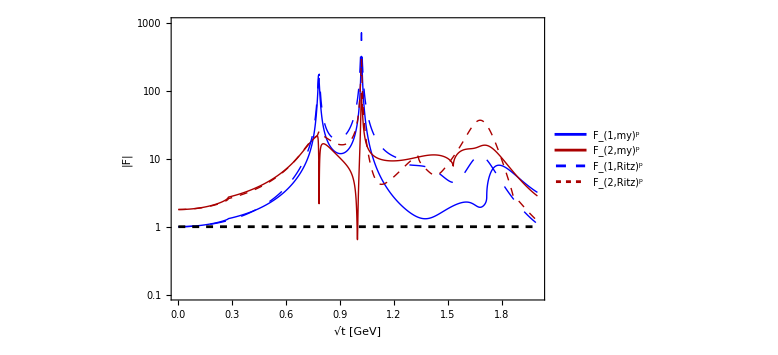

```mathematica
FormFactorsRitz[mX_]=Import[FileNameJoin[{NotebookDirectory[],"FR-form-factors-total.mx"}],"MX"];
{F1Ritz[mX_],F2Ritz[mX_]}={FormFactorsRitz[mX][[2]],FormFactorsRitz[mX][[5]]};
LogPlot[Evaluate[Abs[#]&/@{F1centralInt[pt,m^2],F2centralInt[pt,m^2],F1Ritz[m],F2Ritz[m],1}],{m,0,2},PlotRange->{{0,2},{0.1,1000}},ImageSize->Large,Frame->True,PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.01]},{Dashed,Black},{None}},PlotLegends->Placed[Style[#,18]&/@{Subsuperscript["F","1,my","p"],Subsuperscript["F","2,my","p"],Subsuperscript["F","1,Ritz","p"],Subsuperscript["F","2,Ritz","p"]},Right],PlotPoints->800,FrameStyle->Directive[Black,Thick],LabelStyle->Directive[Black,18],FrameLabel->{"√t [GeV]","|F|"}]
```

#### G_E

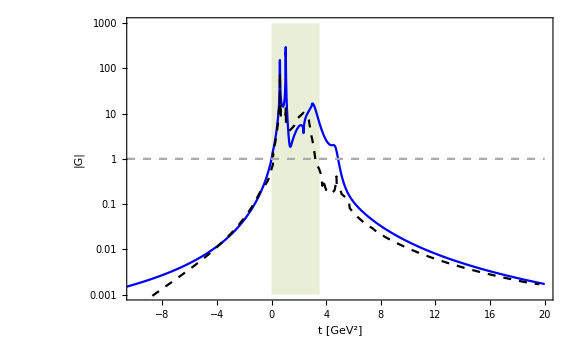
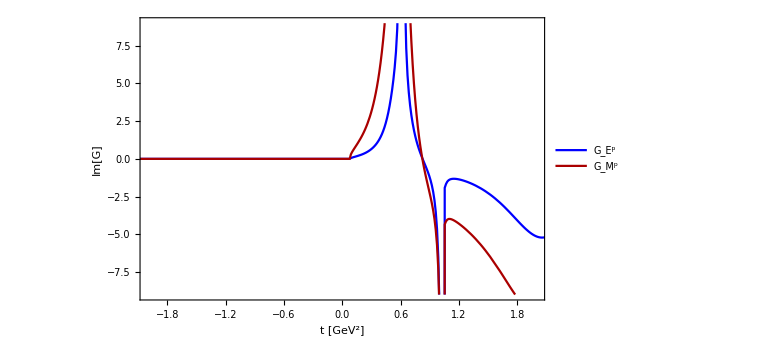

```mathematica
ptformfactor=LogPlot[Evaluate[{Abs[Gep[t]],1,If[0<t<4*0.938^2,100000,0]}],{t,-20,20},PlotRange->{{-10,20},{10^-3,1000}},ImageSize->Large,Frame->True,Filling->{3->Bottom},PlotStyle->{{Thick,Blue},{Lighter@Gray,Dashing[0.01]},{None}},PlotLegends->Placed[Style[#,24]&/@{Subsuperscript["G","E","p"]},{0.8,0.8}],PlotPoints->800,FrameStyle->Directive[Black,Thick],LabelStyle->Directive[Black,18],FrameLabel->{"t [GeV^2]","|G|"}];
EMformFactorData=SortBy[Import[FileNameJoin[{NotebookDirectory[],"EM-form-factor.txt"}],"Table"],#[[1]]&];
ptformfactorX=ListLogPlot[EMformFactorData,PlotRange->{{-10,20},{10^-4,1000}},ImageSize->Large,Frame->True,Filling->{3->Bottom},Joined->True,PlotStyle->{{Thick,Black,Dashing[0.01]},{None}},PlotLegends->Placed[Style[#,24]&/@{Subsuperscript["G","E,Dubnicka","p"]},{0.8,0.8}],FrameStyle->Directive[Black,Thick],LabelStyle->Directive[Black,18],FrameLabel->{"t [GeV^2]","|G^p|"}];
pt3=Show[ptformfactor,ptformfactorX];
ptformfactor=Plot[Evaluate[{Im[Gep[t]],Im[Gmp[t]]}],{t,-20,20},PlotRange->{{-2,2},{-9,9}},ImageSize->Large,Frame->True,Filling->{3->Bottom},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{None}},PlotLegends->Placed[Style[#,24]&/@{Subsuperscript["G","E","p"],Subsuperscript["G","M","p"]},{0.8,0.8}],FrameStyle->Directive[Black,Thick],LabelStyle->Directive[Black,18],FrameLabel->{"t [GeV^2]","Im[G]"}];
Style[Row[{pt3,ptformfactor}],ImageSizeMultipliers->{1, 1}]
```

### Form-factors uncertainties

```mathematica
ranges={"Central","Lower","Upper"};
vars=Flatten[Table[{mρval["Central"],mρprval[c2],mρprprval[c3],mϕval["Central"],mϕprval[c4],mϕprprval[c5],mωval["Central"],mωprval[c6],mωprprval[c7],Γρval["Central"],Γρprval[c8],Γρprprval[c9],Γϕval["Central"],Γϕprval[c10],Γϕprprval[c11],Γωval["Central"],Γωprval[c12],Γωprprval[c13]},{c2,ranges},{c3,ranges},{c4,ranges},{c5,ranges},{c6,ranges},{c7,ranges},{c8,ranges},{c9,ranges},{c10,ranges},{c11,ranges},{c12,ranges},{c13,ranges}],{1,2,3,4,5,6,7,8,9,10,11,12}];
mrange=Table[m,{m,0.02,4,0.03}];
```

### Finding min/max value

{True,{}}

Generating uncertainty band...

{105.29,Null}

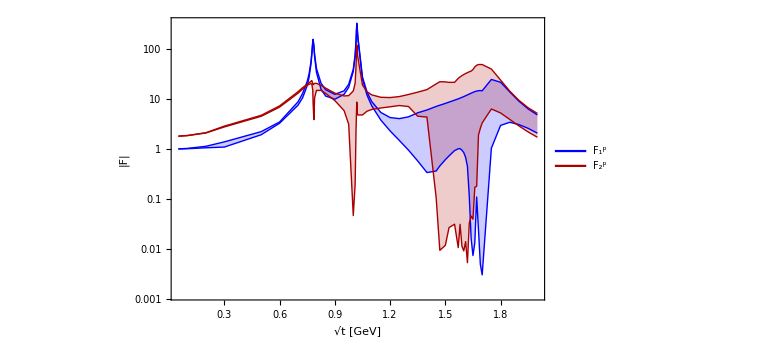

```mathematica
checkIfCompiled[compiledFunc_CompiledFunction]:=Module[{compiledPrintOutput,hasMainEvaluate,mainEvaluateParts},compiledPrintOutput=ToString[CompiledFunctionTools`CompilePrint[compiledFunc],InputForm];
hasMainEvaluate=StringContainsQ[compiledPrintOutput,"MainEvaluate"];
mainEvaluateParts=If[hasMainEvaluate,StringCases[compiledPrintOutput,"MainEvaluate"~~"["~~Shortest[___]~~"]"],{}];
{!hasMainEvaluate,mainEvaluateParts}]
<<CompiledFunctionTools`
(*CompilePrint@minmaxcode*)
minmaxcode=Hold@Compile[{{mrange,_Complex,1},{j,_Integer},{vars,_Real,2}},Module[{tabvalsF1,tabvalsF2,max=0.,min=10^8.,val1,val2,el=0.+0.*I,valmin=0.+0.*I,valmax=0.+0.*I,valminF2=0.+0.*I,valmaxF2=0.+0.*I,elabs=0.,m=Compile`GetElement[mrange,j]},tabvalsF1=Table[F1totalTemp[m^2,Compile`GetElement[vars,i,1],Compile`GetElement[vars,i,2],Compile`GetElement[vars,i,3],Compile`GetElement[vars,i,4],Compile`GetElement[vars,i,5],Compile`GetElement[vars,i,6],Compile`GetElement[vars,i,7],Compile`GetElement[vars,i,8],Compile`GetElement[vars,i,9],Compile`GetElement[vars,i,10],Compile`GetElement[vars,i,11],Compile`GetElement[vars,i,12],Compile`GetElement[vars,i,13],Compile`GetElement[vars,i,14],Compile`GetElement[vars,i,15],Compile`GetElement[vars,i,16],Compile`GetElement[vars,i,17],Compile`GetElement[vars,i,18]],{i,1,Length[vars]}];
tabvalsF2=Table[F2totalTemp[m^2,Compile`GetElement[vars,i,1],Compile`GetElement[vars,i,2],Compile`GetElement[vars,i,3],Compile`GetElement[vars,i,4],Compile`GetElement[vars,i,5],Compile`GetElement[vars,i,6],Compile`GetElement[vars,i,7],Compile`GetElement[vars,i,8],Compile`GetElement[vars,i,9],Compile`GetElement[vars,i,10],Compile`GetElement[vars,i,11],Compile`GetElement[vars,i,12],Compile`GetElement[vars,i,13],Compile`GetElement[vars,i,14],Compile`GetElement[vars,i,15],Compile`GetElement[vars,i,16],Compile`GetElement[vars,i,17],Compile`GetElement[vars,i,18]],{i,1,Length[vars]}];
Do[
el=Compile`GetElement[tabvalsF1,k];
elabs=Abs[el];
If[elabs<min,
min=elabs;
valmin=el;
];
If[elabs>max,
max=elabs;
valmax=el;
]
,{k,1,Length[tabvalsF1],1}];
max=0.;
min=10^8.;
Do[
el=Compile`GetElement[tabvalsF2,k];
elabs=Abs[el];
If[elabs<min,
min=elabs;
valminF2=el;
];
If[elabs>max,
max=elabs;
valmaxF2=el;
]
,{k,1,Length[tabvalsF2],1}];
{m,valmin,valmax,valminF2,valmaxF2}
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True]/. DownValues@F1totalTemp/. DownValues@F2totalTemp//ReleaseHold;
checkIfCompiled[minmaxcode]
(*minmaxcodeTotal=With[{minmaxc=minmaxcode},Hold@Compile[{{mrange,_Complex,1},{vars,_Real,2}},
Table[minmaxc[mrange,j,vars],{j,1,Length[mrange],1}]
,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True,CompilationOptions->{"InlineCompiledFunctions"->True}]//ReleaseHold];
checkIfCompiled[minmaxcodeTotal]*)
minmaxcodeTotal[mrange_,vars_]:=ParallelTable[minmaxcode[mrange,j,vars],{j,1,Length[mrange],1}];
Print["Generating uncertainty band..."]
mrange={0.05,0.1,0.2,0.3,0.5,0.6,0.7,0.725,0.75,0.76,0.77,0.775,0.78,0.782,0.786,0.79,0.8,0.825,0.85,0.9,0.95,0.975,1.,1.01,1.015,1.019,1.022,1.025,1.05,1.075,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.47,1.5,1.52,1.55,1.57,1.58,1.59,1.6,1.61,1.62,1.63,1.64,1.65,1.66,1.67,1.68,1.69,1.7,1.75,1.8,1.85,1.9,1.95,2.};
test=minmaxcodeTotal[mrange,vars];//AbsoluteTiming
Show[ListLogPlot[{{#[[1]],Abs[#[[2]]]}&/@test,{#[[1]],Abs[#[[3]]]}&/@test,{#[[1]],Abs[#[[4]]]}&/@test,{#[[1]],Abs[#[[5]]]}&/@test},PlotRange->{MinMax[Re[test[[All,1]]]],All},Joined->True,ImageSize->Large,Frame->True,FrameStyle->Directive[Thick,Black],PlotStyle->{{Thick,Blue},{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Red}},Filling->{1->{2},3->{4}},LabelStyle->Directive[Black,18],FrameLabel->{"√t [GeV]","|F|"}],LogPlot[{10^9,10^9},{t,10^-3.,10},PlotRange->{MinMax[Re[test[[All,1]]]],All},ImageSize->Large,Frame->True,FrameStyle->Directive[Thick,Black],PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Red}},Filling->{1->{2},3->{4}},LabelStyle->Directive[Black,18],FrameLabel->{"√t [GeV]","|F|"},PlotLegends->Placed[Style[#,24]&/@{Subsuperscript["F","1","p"],Subsuperscript["F","2","p"]},{0.2,0.8}]]]
```

## Case study - dark photon 1

### Isovector and isoscalar form-factors as functions of t_in and f_VNN

```mathematica
pt="DP";
(*Values of parameters from Dubnicka's paper*)
MapThread[(f1val[pt,w,#1]=#2)&,{{0,1},{1.5717,0.0418}}];
MapThread[(f1val[pt,p,#1]=#2)&,{{0,1},{-1.1247,0.1879}}];
MapThread[(f1val[pt,r,#1]=#2)&,{{0},{0.3747}}];
MapThread[(f2val[pt,w,#1]=#2)&,{{0},{-0.2096}}];
MapThread[(f2val[pt,p,#1]=#2)&,{{0,1},{0.2657,0.1781}}];
{tin1val["s"],tin2val["s"],tin1val["v"],tin2val["v"]}={1.0442,1.046,2.9506,2.3449};
{F01val["s",pt],F02val["s",pt],F01val["v",pt],F02val["v",pt]}={1/2,1/2(μp+μn-1),1/2,1/2(μp-μn-1)};
F1toFit[pt,"s",t_,f1ϕ_,f1ϕpr_,f1ω_,f1ωpr_,tin1s_]=F1conf["s",t,mϕval["Central"],mϕprval["Central"],mϕprprval["Central"],mωval["Central"],mωprval["Central"],mωprprval["Central"],Γϕval["Central"],Γϕprval["Central"],Γϕprprval["Central"],Γωval["Central"],Γωprval["Central"],Γωprprval["Central"],F01val["s",pt],f1ϕ,f1ϕpr,f1ω,f1ωpr,tin1s];
F2toFit[pt,"s",t_,f2ϕ_,f2ϕpr_,f2ω_,tin2s_]=F2conf["s",t,mϕval["Central"],mϕprval["Central"],mϕprprval["Central"],mωval["Central"],mωprval["Central"],mωprprval["Central"],Γϕval["Central"],Γϕprval["Central"],Γϕprprval["Central"],Γωval["Central"],Γωprval["Central"],Γωprprval["Central"],F02val["s",pt],f2ϕ,f2ϕpr,f2ω,f2ωpr,tin2s];
F1toFit[pt,"v",t_,f1ρ_,fρprNN_,tin1v_]=F1conf["v",t,mρval["Central"],mρprval["Central"],mρprprval["Central"],Γρval["Central"],Γρprval["Central"],Γρprprval["Central"],F01val["v",pt],f1ρ,fρprNN,tin1v];
F2toFit[pt,"v",t_,tin2v_]=F2conf["v",t,mρval["Central"],mρprval["Central"],mρprprval["Central"],Γρval["Central"],Γρprval["Central"],Γρprprval["Central"],F02val["v",pt],f2val[pt,r,0],fρprNN,tin2v];
F1toFitTotal[t_,f1ρ_,f1ϕ_,f1ϕpr_,f1ω_,f1ωpr_,tin1s_,tin1v_]=F1toFit[pt,"s",t,f1ϕ,f1ϕpr,f1ω,f1ωpr,tin1s]+F1toFit[pt,"v",t,f1ρ,fρprNN,tin1v];
F2toFitTotal[t_,f2ϕ_,f2ϕpr_,f2ω_,tin2s_,tin2v_]=F2toFit[pt,"s",t,f2ϕ,f2ϕpr,f2ω,tin2s]+F2toFit[pt,"v",t,tin2v];
```

### Fitting to Ritz’s curves

{98.7168,Null}

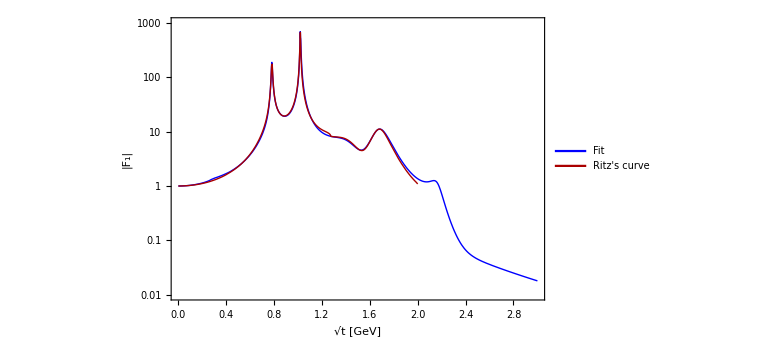

Set | f_ϕNN | f_(ϕ' NN) | f_ωNN | f_(ω' NN) | f_ρNN | t_(in, s) | t_(in, v)
Fit to Ritz's curve | -2.40814 | 0.772547 | 1.9326 | 1.39609 | 0.616018 | 1.04423 | 2.82028
Dubnicka | -1.1247 | 0.1879 | 1.5717 | 0.0418 | 0.3747 | 1.0442 | 2.9506

```mathematica
(*ptsdataset=Table[{RandomReal[{0.4,0.6}],RandomReal[{0.8,0.9}],RandomReal[{1.2,1.4}],RandomReal[{1.65,1.75}],RandomReal[{1.9,1.99}],RandomReal[{1.04,1.05}],RandomReal[{2.8,3.1}]},500];*)
ptsdataset=Table[{RandomReal[{0.4,0.6}],RandomReal[{0.8,0.9}],RandomReal[{0.9,1.65}],RandomReal[{1.65,1.75}],RandomReal[{1.75,1.99}],RandomReal[{1.04,1.05}],RandomReal[{2.8,3.1}]},1000];
vall[mX_,tin1s_,tin1v_]:=(ComplexExpand[F1toFitTotal[mX^2,f1ρ,f1ϕ,f1ϕpr,f1ω,f1ωpr,tin1s,tin1v]]/.{a_+I*b_:>Sqrt[a^2+b^2]})==Abs[F1Ritz[mX]]
fvals[pts_,i_]:=Block[{},
{masses,tins1,tinv1}={Take[pts[[i]],{1,5}],pts[[i]][[-2]],pts[[i]][[-1]]};
Eqs=Table[vall[mX,tins1,tinv1],{mX,masses}];
soll1=FindRoot[Eqs,Evaluate[{{f1ϕ,f1val[pt,p,0]},{f1ϕpr,f1val[pt,p,1]},{f1ω,f1val[pt,w,0]},{f1ωpr,f1val[pt,w,1]},{f1ρ,f1val[pt,r,0]}}],MaxIterations->100000,AccuracyGoal->20,PrecisionGoal->20];
{f1ϕfit,f1ϕprfit,f1ωfit,f1ωprfit,f1ρfit}={f1ϕ,f1ϕpr,f1ω,f1ωpr,f1ρ}/.soll1;
F1form[mX_]=F1toFitTotal[mX^2,f1ρfit,f1ϕfit,f1ϕprfit,f1ωfit,f1ωprfit,tins1,tinv1];
deviations=Sum[(Abs[F1form[mX]]-Abs[F1Ritz[mX]])^2/Abs[F1Ritz[mX]]^2,{mX,Table[x,{x,0.209,1.999,0.01}]}];
{f1ϕfit,f1ϕprfit,f1ωfit,f1ωprfit,f1ρfit,tins1,tinv1,F1form[mX],deviations}
]
solS[mX_]=SortBy[ParallelTable[Quiet[fvals[ptsdataset,i]],{i,1,Length[ptsdataset],1}],#[[-1]]&];//AbsoluteTiming
LogPlot[Evaluate[{Abs[solS[mX][[1]][[-2]]],If[mX<=2,Evaluate[Abs[F1Ritz[mX]]],0.]}],{mX,0.001,3.},PlotRange->{{0.001,3.},{0.01,1000}},ImageSize->Large,Frame->True,Filling->{3->Bottom},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{None}},PlotLegends->Placed[Style[#,24]&/@{"Fit","Ritz's curve"},{0.8,0.8}],FrameStyle->Directive[Black,Thick],LabelStyle->Directive[Black,18],FrameLabel->{"√t [GeV]","|F_1|"}]
{{"Set","f_ϕNN","f_(ϕ' NN)","f_ωNN","f_(ω' NN)","f_ρNN","t_(in, s)","t_(in, v)"},Join[{"Fit to Ritz's curve"},Drop[solS[mX][[1]],-2]],{"Dubnicka",f1val[pt,p,0],f1val[pt,p,1],f1val[pt,w,0],f1val[pt,w,1],f1val[pt,r,0],tin1val["s"],tin1val["v"]}}//TableForm
```

{98.7477,Null}

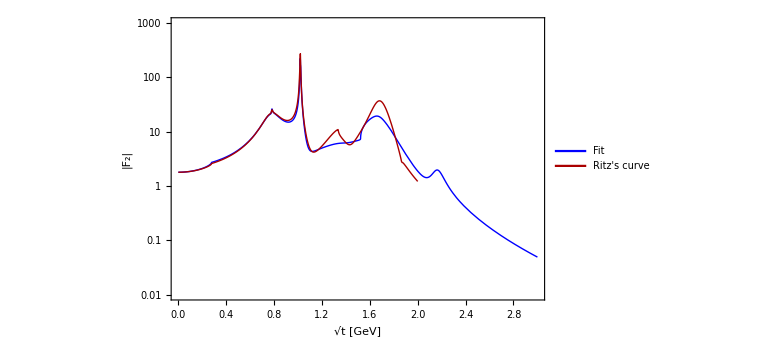

Set | f_ϕNN | f_(ϕ' NN) | f_ωNN | t_(in, s) | t_(in, v)
Fit to Ritz's curve | -0.632036 | -0.179361 | 0.0515459 | 1.04407 | 2.32002
Dubnicka | 0.2657 | 0.1781 | -0.2096 | 1.046 | 2.3449

```mathematica
(*ptsdataset=Table[{RandomReal[{0.4,0.9}],RandomReal[{1.17,1.45}],RandomReal[{1.5,1.99}],RandomReal[{1.04,1.05}],RandomReal[{2.32,2.36}]},5000];*)
(*ptsdataset=Table[{RandomReal[{0.76,0.8}],RandomReal[{1.07,1.5}],RandomReal[{1.88,1.9}],RandomReal[{1.04,1.05}],RandomReal[{2.32,2.36}]},2000];*)
ptsdataset=Table[{RandomReal[{0.76,1.07}],RandomReal[{1.07,1.5}],RandomReal[{1.5,1.7}],RandomReal[{1.04,1.05}],RandomReal[{2.32,2.36}]},2000];

vall[mX_,tin2s_,tin2v_]:=Log[(ComplexExpand[F2toFitTotal[mX^2,f2ϕ,f2ϕpr,f2ω,tin2s,tin2v]]/.{a_+I*b_:>Sqrt[a^2+b^2]})/Abs[F2Ritz[mX]]]==0
mrangedeviations=Table[x,{x,0.209,1.999,0.01}];
fvals[pts_,i_]:=Module[{},
{masses,tin2sfit,tin2vfit}={Take[pts[[i]],{1,3}],pts[[i]][[-2]],pts[[i]][[-1]]};
Eqs=Table[vall[mX,tin2sfit,tin2vfit],{mX,masses}];
soll1=FindRoot[Eqs,Evaluate[{{f2ϕ,f2val[pt,p,0]},{f2ϕpr,f2val[pt,p,1]},{f2ω,f2val[pt,w,0]}}],MaxIterations->100000,AccuracyGoal->30,PrecisionGoal->30];
{f2ϕfit,f2ϕprfit,f2ωfit}={f2ϕ,f2ϕpr,f2ω}/.soll1;
F2form[mX_]=F2toFitTotal[mX^2,f2ϕfit,f2ϕprfit,f2ωfit,tin2sfit,tin2vfit];

deviations=Sum[(Abs[F2form[mX]]-Abs[F2Ritz[mX]])^2/Abs[F2Ritz[mX]]^2,{mX,mrangedeviations}](**Sum[(Abs[F2form[mX]]-Abs[F2Ritz[mX]])^2/Abs[F2Ritz[mX]],{mX,{0.782,1.34,1.67,1.86,1.99}}]*);
{f2ϕfit,f2ϕprfit,f2ωfit,tin2sfit,tin2vfit,F2form[mX],deviations}
]
solS2[mX_]=SortBy[ParallelTable[Quiet[fvals[ptsdataset,i]],{i,1,Length[ptsdataset],1}],#[[-1]]&];//AbsoluteTiming
LogPlot[Evaluate[{Abs[solS2[mX][[1]][[-2]]],If[mX<=2,Evaluate[Abs[F2Ritz[mX]]],0.]}],{mX,0.001,3.},PlotRange->{{0.001,3.},{0.01,1000}},ImageSize->Large,Frame->True,Filling->{3->Bottom},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{None}},PlotLegends->Placed[Style[#,24]&/@{"Fit","Ritz's curve"},{0.8,0.8}],FrameStyle->Directive[Black,Thick],LabelStyle->Directive[Black,18],FrameLabel->{"√t [GeV]","|F_2|"}]
{{"Set","f_ϕNN","f_(ϕ' NN)","f_ωNN","t_(in, s)","t_(in, v)"},Join[{"Fit to Ritz's curve"},Drop[solS2[mX][[1]],-2]],{"Dubnicka",f2val[pt,p,0],f2val[pt,p,1],f2val[pt,w,0],tin2val["s"],tin2val["v"]}}//TableForm
```

```mathematica
masses
```

{0.789325,1.35013,1.89095}

```mathematica
fvals[ptsdataset,1];
soll1
{masses[[#]],Abs[F2form[masses[[#]]]],Abs[F2Ritz[masses[[#]]]]}&/@Range[1,3]
```

{f2ϕ→-0.567422,f2ϕpr→-0.10698,f2ω→0.286735}

{{0.906073,16.1375,16.1375},{1.224,6.22944,6.22944},{1.51981,9.72835,9.72835}}

### Total form factors

```mathematica
valslist={mρval["Central"],mρprval["Central"],mρprprval["Central"],mϕval["Central"],mϕprval["Central"],mϕprprval["Central"],mωval["Central"],mωprval["Central"],mωprprval["Central"],Γρval["Central"],Γρprval["Central"],Γρprprval["Central"],Γϕval["Central"],Γϕprval["Central"],Γϕprprval["Central"],Γωval["Central"],Γωprval["Central"],Γωprprval["Central"]};
pt="DP";
F1total[pt,"Arbitrary",t_,mρ_,mρpr_,mρprpr_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γρ_,Γρpr_,Γρprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_]=F1totalTemp[t_,mρ_,mρpr_,mρprpr_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γρ_,Γρpr_,Γρprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_]=F1conf[pt,"s",t,mϕ,mϕpr,mϕprpr,mω,mωpr,mωprpr,Γϕ,Γϕpr,Γϕprpr,Γω,Γωpr,Γωprpr]+F1conf[pt,"v",t,mρ,mρpr,mρprpr,Γρ,Γρpr,Γρprpr];
F2total[pt,"Arbitrary",t_,mρ_,mρpr_,mρprpr_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γρ_,Γρpr_,Γρprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_]=F2totalTemp[t_,mρ_,mρpr_,mρprpr_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γρ_,Γρpr_,Γρprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_]=F2conf[pt,"s",t,mϕ,mϕpr,mϕprpr,mω,mωpr,mωprpr,Γϕ,Γϕpr,Γϕprpr,Γω,Γωpr,Γωprpr]+F2conf[pt,"v",t,mρ,mρpr,mρprpr,Γρ,Γρpr,Γρprpr];
{F1central[pt,t_],F2central[pt,t_]}={F1centralTemp[t_],F2centralTemp[t_]}=(#@@Join[{pt,"Arbitrary",t},valslist])&/@{F1total,F2total};
FFtab=Hold@Compile[{{massrange,_Complex}},{F1centralTemp[massrange],F2centralTemp[massrange]},CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True]/.DownValues@F1centralTemp/.DownValues@F2centralTemp//ReleaseHold;
massrange=Table[m,{m,-49.,49.,0.001}];
{F1centralInt[pt,t_],F2centralInt[pt,t_]}=With[{tab=FFtab[massrange]},Interpolation[Join[Partition[massrange,1],tab[[All,{#}]],2],InterpolationOrder->1][t]]&/@{1,2};//AbsoluteTiming
{Gep[t_],Gmp[t_]}={F1centralInt[pt,t]+t/(4*0.938^2)F2centralInt[pt,t],F1centralInt[pt,t]+F2centralInt[pt,t]};
```

{0.408612,Null}

## Case study - B-L

### Rescaling couplings

```mathematica
θmix=3.32*Pi/180;
qgen=1/2 DiagonalMatrix[{1,1,0}];
sgen=1/(√2)DiagonalMatrix[{0,0,1}];
Tϕ=Sin[θmix]*qgen-Cos[θmix]*sgen;
Tω=Sin[θmix]sgen+Cos[θmix]qgen;
Qp=1/3 DiagonalMatrix[{2,-1,-1}];
{RescalingCoeff[w],RescalingCoeff[p]}=1/3{Tr[Tω]/Tr[Tω.Qp],Tr[Tϕ]/Tr[Tϕ.Qp]};
pt="B";
MapThread[(f1val[pt,w,#1]=#2)&,{{0,1},RescalingCoeff[w]{1.5717,0.0418}}];
MapThread[(f1val[pt,p,#1]=#2)&,{{0,1},RescalingCoeff[p]{-1.1247,0.1879}}];
MapThread[(f1val[pt,r,#1]=#2)&,{{0},{0.}}];
MapThread[(f2val[pt,w,#1]=#2)&,{{0},RescalingCoeff[w]{-0.2096}}];
MapThread[(f2val[pt,p,#1]=#2)&,{{0,1},RescalingCoeff[p]{0.2657,0.1781}}];
{tin1val["s"],tin2val["s"],tin1val["v"],tin2val["v"]}={1.0442,1.046,2.9506,2.3449};
μs=-0.064;
{F01val["s",pt],F02val["s",pt],F01val["v",pt],F02val["v",pt]}={1,1/3(2(μp-1)+μn+μs)+1/3(2μn+(μp-1)+μs),0.,0.}
```

{1,-0.163667,0.,0.}

### Form-factors

```mathematica
F1conf[pt,"s",t_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_]=F1temp[t_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_]=F1conf["s",t,mϕ,mϕpr,mϕprpr,mω,mωpr,mωprpr,Γϕ,Γϕpr,Γϕprpr,Γω,Γωpr,Γωprpr,F01val["s",pt],f1val[pt,p,0],f1val[pt,p,1],f1val[pt,w,0],f1val[pt,w,1],tin1val["s"]];
F2conf[pt,"s",t_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_]=F2temp[t_,mϕ_,mϕpr_,mϕprpr_,mω_,mωpr_,mωprpr_,Γϕ_,Γϕpr_,Γϕprpr_,Γω_,Γωpr_,Γωprpr_]=F2conf["s",t,mϕ,mϕpr,mϕprpr,mω,mωpr,mωprpr,Γϕ,Γϕpr,Γϕprpr,Γω,Γωpr,Γωprpr,F02val["s",pt],f2val[pt,p,0],f2val[pt,p,1],f2val[pt,w,0],f2val[pt,w,1],tin2val["s"]];
ranges={"Central","Lower","Upper"};
vars=Flatten[Table[{mϕval["Central"],mϕprval[c2],mϕprprval[c3],mωval["Central"],mωprval[c4],mωprprval[c5],Γϕval["Central"],Γϕprval[c6],Γϕprprval[c7],Γωval["Central"],Γωprval[c8],Γωprprval[c9]},{c2,ranges},{c3,ranges},{c4,ranges},{c5,ranges},{c6,ranges},{c7,ranges},{c8,ranges},{c9,ranges}],{1,2,3,4,5,6,7,8}];
mrange=Table[m,{m,0.02,4,0.01}];
```

```mathematica
ranges
```

{Central,Lower,Upper}

### Finding min/max value

```mathematica
checkIfCompiled[compiledFunc_CompiledFunction]:=Module[{compiledPrintOutput,hasMainEvaluate,mainEvaluateParts},compiledPrintOutput=ToString[CompiledFunctionTools`CompilePrint[compiledFunc],InputForm];
hasMainEvaluate=StringContainsQ[compiledPrintOutput,"MainEvaluate"];
mainEvaluateParts=If[hasMainEvaluate,StringCases[compiledPrintOutput,"MainEvaluate"~~"["~~Shortest[___]~~"]"],{}];
{!hasMainEvaluate,mainEvaluateParts}]
<<CompiledFunctionTools`
(*CompilePrint@minmaxcode*)
checkIfCompiled[minmaxcode]
minmaxcode=Hold@Compile[{{mrange,_Complex,1},{j,_Integer},{vars,_Real,2}},Module[{tabvalsF1,tabvalsF2,max=0.,min=10^8.,val1,val2,el=0.+0.*I,valmin=0.+0.*I,valmax=0.+0.*I,valminF2=0.+0.*I,valmaxF2=0.+0.*I,elabs=0.,m=Compile`GetElement[mrange,j]},tabvalsF1=Table[F1temp[m^2,Compile`GetElement[vars,i,1],Compile`GetElement[vars,i,2],Compile`GetElement[vars,i,3],Compile`GetElement[vars,i,4],Compile`GetElement[vars,i,5],Compile`GetElement[vars,i,6],Compile`GetElement[vars,i,7],Compile`GetElement[vars,i,8],Compile`GetElement[vars,i,9],Compile`GetElement[vars,i,10],Compile`GetElement[vars,i,11],Compile`GetElement[vars,i,12]],{i,1,Length[vars]}];
tabvalsF2=Table[F2temp[m^2,Compile`GetElement[vars,i,1],Compile`GetElement[vars,i,2],Compile`GetElement[vars,i,3],Compile`GetElement[vars,i,4],Compile`GetElement[vars,i,5],Compile`GetElement[vars,i,6],Compile`GetElement[vars,i,7],Compile`GetElement[vars,i,8],Compile`GetElement[vars,i,9],Compile`GetElement[vars,i,10],Compile`GetElement[vars,i,11],Compile`GetElement[vars,i,12]],{i,1,Length[vars]}];
Do[
el=Compile`GetElement[tabvalsF1,k];
elabs=Abs[el];
If[elabs<min,
min=elabs;
valmin=el;
];
If[elabs>max,
max=elabs;
valmax=el;
]
,{k,1,Length[tabvalsF1],1}];
max=0.;
min=10^8.;
Do[
el=Compile`GetElement[tabvalsF2,k];
elabs=Abs[el];
If[elabs<min,
min=elabs;
valminF2=el;
];
If[elabs>max,
max=elabs;
valmaxF2=el;
]
,{k,1,Length[tabvalsF2],1}];
{m,valmin,valmax,valminF2,valmaxF2}
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True]/. DownValues@F1temp/. DownValues@F2temp//ReleaseHold;
minmaxcodeTotal=With[{minmaxc=minmaxcode},Hold@Compile[{{mrange,_Complex,1},{vars,_Real,2}},
Table[minmaxc[mrange,j,vars],{j,1,Length[mrange],1}]
,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True,CompilationOptions->{"InlineCompiledFunctions"->True}]//ReleaseHold];
checkIfCompiled[minmaxcodeTotal]
```

checkIfCompiled(minmaxcode)

{True,{}}

```mathematica
test=minmaxcodeTotal[mrange,vars];//AbsoluteTiming
```

{12.0198,Null}

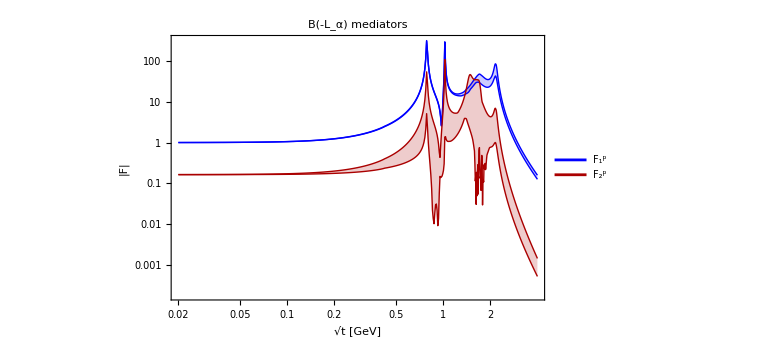

```mathematica
Show[ListLogLogPlot[{{#[[1]],Abs[#[[2]]]}&/@test,{#[[1]],Abs[#[[3]]]}&/@test,{#[[1]],Abs[#[[4]]]}&/@test,{#[[1]],Abs[#[[5]]]}&/@test},PlotRange->{MinMax[Re[test[[All,1]]]],All},Joined->True,ImageSize->Large,Frame->True,FrameStyle->Directive[Thick,Black],PlotStyle->{{Thick,Blue},{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Red}},Filling->{1->{2},3->{4}},FrameLabel->{"√t [GeV]","|F|"},LabelStyle->Directive[Black,18],PlotLabel->Row[{"B(-L_α) mediators"}]],LogLogPlot[{100000t,100000t},{t,0.1,2},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Red}},PlotLegends->Placed[Style[#,24]&/@{Subsuperscript["F","1","p"],Subsuperscript["F","2","p"]},{0.2,0.8}]]]
```

### Plot

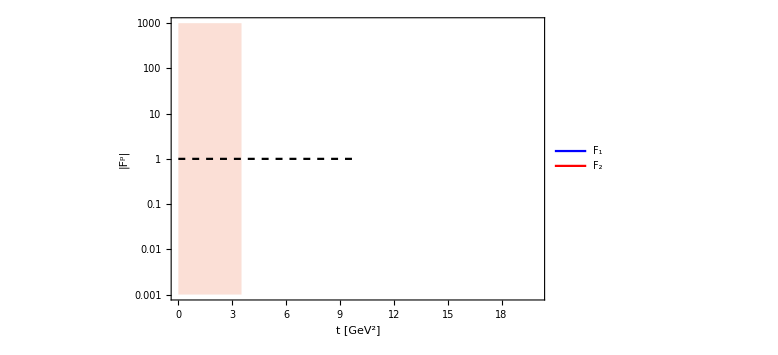

```mathematica
ptformfactor=LogPlot[Evaluate[{Abs[F1conf[pt,"s",t]],Abs[F2conf[pt,"s",t]],1,If[0<t<4*0.938^2,100000,0]}],{t,0,10},PlotRange->{{0,20},{10^-3,1000}},ImageSize->Large,Frame->True,Filling->{4->Bottom},PlotStyle->{{Thick,Blue},{Thick,Red},{Dashed,Black},{None}},PlotLegends->Placed[Style[#,24]&/@{"F_1","F_2"},{0.8,0.8}],PlotPoints->800,FrameStyle->Directive[Black,Thick],LabelStyle->Directive[Black,18],FrameLabel->{"t [GeV^2]","|F^p|"}]
```

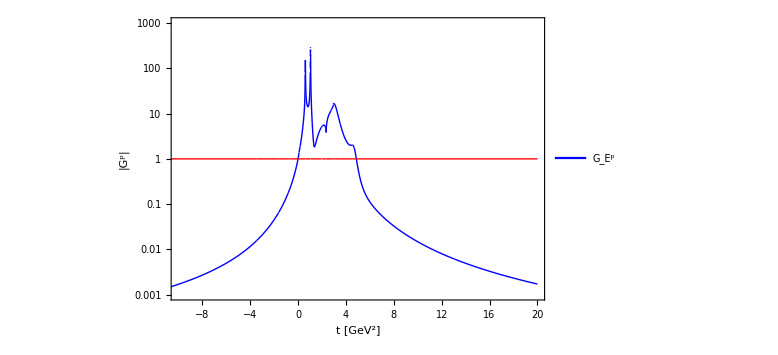

```mathematica
Gep[t_]=F1conf["DP","s",t,mϕval["Central"],mϕprval["Central"],mϕprprval["Central"],mωval["Central"],mωprval["Central"],mωprprval["Central"],Γϕval["Central"],Γϕprval["Central"],Γϕprprval["Central"],Γωval["Central"],Γωprval["Central"],Γωprprval["Central"]]+F1conf["DP","v",t,mρval["Central"],mρprval["Central"],mρprprval["Central"],Γρval["Central"],Γρprval["Central"],Γρprprval["Central"]]+t/(4*0.938^2)(F2conf["DP","s",t,mϕval["Central"],mϕprval["Central"],mϕprprval["Central"],mωval["Central"],mωprval["Central"],mωprprval["Central"],Γϕval["Central"],Γϕprval["Central"],Γϕprprval["Central"],Γωval["Central"],Γωprval["Central"],Γωprprval["Central"]]+F2conf["DP","v",t,mρval["Central"],mρprval["Central"],mρprprval["Central"],Γρval["Central"],Γρprval["Central"],Γρprprval["Central"]]);
Gmp[t_]=F1conf["DP","s",t,mϕval["Central"],mϕprval["Central"],mϕprprval["Central"],mωval["Central"],mωprval["Central"],mωprprval["Central"],Γϕval["Central"],Γϕprval["Central"],Γϕprprval["Central"],Γωval["Central"],Γωprval["Central"],Γωprprval["Central"]]+F1conf["DP","v",t,mρval["Central"],mρprval["Central"],mρprprval["Central"],Γρval["Central"],Γρprval["Central"],Γρprprval["Central"]]+(F2conf["DP","s",t,mϕval["Central"],mϕprval["Central"],mϕprprval["Central"],mωval["Central"],mωprval["Central"],mωprprval["Central"],Γϕval["Central"],Γϕprval["Central"],Γϕprprval["Central"],Γωval["Central"],Γωprval["Central"],Γωprprval["Central"]]+F2conf["DP","v",t,mρval["Central"],mρprval["Central"],mρprprval["Central"],Γρval["Central"],Γρprval["Central"],Γρprprval["Central"]]);
```

```mathematica
EMformFactorData=SortBy[Import[FileNameJoin[{NotebookDirectory[],"EM-form-factor.txt"}],"Table"],#[[1]]&];
```

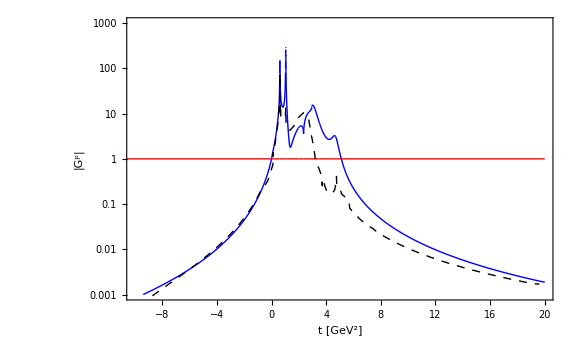

```mathematica
ptformfactorX=ListLogPlot[EMformFactorData,PlotRange->{{-10,20},{10^-4,1000}},ImageSize->Large,Frame->True,Filling->{3->Bottom},Joined->True,PlotStyle->{{Thick,Black,Dashing[0.01]},{Dashed,Black},{None}},PlotLegends->Placed[Style[#,24]&/@{Subsuperscript["G","E","p"]},{0.8,0.8}],FrameStyle->Directive[Black,Thick],LabelStyle->Directive[Black,18],FrameLabel->{"t [GeV^2]","|G^p|"}];
Show[ptformfactor,ptformfactorX]
```

$Aborted

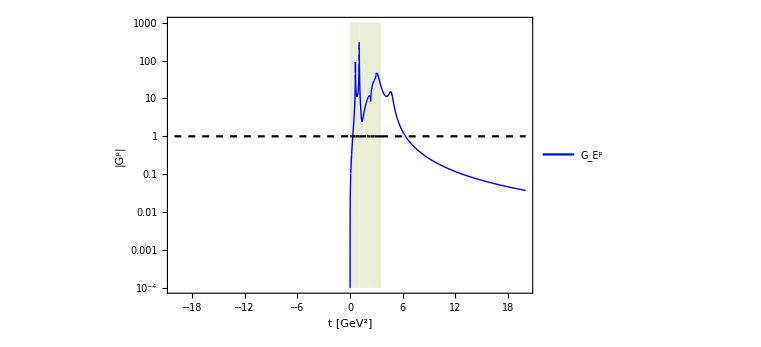

```mathematica
LogPlot[Evaluate[{Im[Gep[t]],1,If[0<t<4*0.938^2,100000,0]}],{t,-20,20},PlotRange->{All,{10^-4,1000}},ImageSize->Large,Frame->True,Filling->{3->Bottom},PlotStyle->{{Thick,Blue},{Dashed,Black},{None}},PlotLegends->Placed[Style[#,24]&/@{Subsuperscript["G","E","p"]},{0.8,0.8}],PlotPoints->800,FrameStyle->Directive[Black,Thick],LabelStyle->Directive[Black,18],FrameLabel->{"t [GeV^2]","|G^p|"}]
```

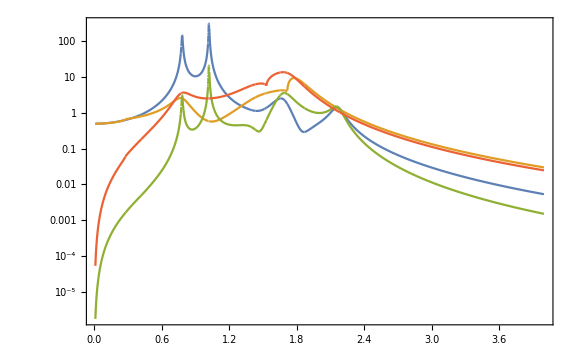

```mathematica
LogPlot[Evaluate[{Abs[F1conf["DP","s",t^2,mϕval["Central"],mϕprval["Central"],mϕprprval["Central"],mωval["Central"],mωprval["Central"],mωprprval["Central"],Γϕval["Central"],Γϕprval["Central"],Γϕprprval["Central"],Γωval["Central"],Γωprval["Central"],Γωprprval["Central"]]],Abs[F1conf["DP","v",t^2,mρval["Central"],mρprval["Central"],mρprprval["Central"],Γρval["Central"],Γρprval["Central"],Γρprprval["Central"]]],Abs[t^2/(4*0.938^2)F2conf["DP","s",t^2,mϕval["Central"],mϕprval["Central"],mϕprprval["Central"],mωval["Central"],mωprval["Central"],mωprprval["Central"],Γϕval["Central"],Γϕprval["Central"],Γϕprprval["Central"],Γωval["Central"],Γωprval["Central"],Γωprprval["Central"]]],Abs[t^2/(4*0.938^2)F2conf["DP","v",t^2,mρval["Central"],mρprval["Central"],mρprprval["Central"],Γρval["Central"],Γρprval["Central"],Γρprprval["Central"]]]}],{t,0.01,4},ImageSize->Large,Frame->True,PlotRange->All,PlotPoints->600]
```

```mathematica
xxx=Import[FileNameJoin[{NotebookDirectory[],"FR-form-factors-total.mx"}],"MX"];
```

```mathematica
xxx[[1]]
```

If[mX<1.989,If[mX<1.99,10^(InterpolatingFunction[…][Log[mX]/Log[10]]),0.],-(1315.14+2216.16 ⅈ)/mX^12]